# Simulating BZ Life Forms using a Phenomenological Model

#### Abhishek Sharma Cronin Lab University of Glasgow

THIS FILE ANALYSES THE GENERATED DATA FROM THE SIMULATION. THE DATA SHOULD BE AT THE RIGHT PATH.

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/

## BZ Life Forms : Population Analysis

```mathematica
nRuns=25;nSteps=15000;
```

```mathematica
analyzeAllData[nLifeForms_,runID_]:=Module[{allPWMStates,allCAStates},
allPWMStates=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[nLifeForms]<>".mx"];
Length[Position[allPWMStates⟦#⟧,3]]&/@Range[nSteps]]
```

```mathematica
popLifeForms1=analyzeAllData[1,#]&/@Range[nRuns];
```

```mathematica
popLifeForms10=analyzeAllData[10,#]&/@Range[nRuns];
```

```mathematica
popLifeForms100=analyzeAllData[100,#]&/@Range[nRuns];
```

```mathematica
popLifeForms1000=analyzeAllData[1000,#]&/@Range[nRuns];
```

```mathematica
Dimensions/@{popLifeForms1,popLifeForms10,popLifeForms100,popLifeForms1000}
```

{{25,15000},{25,15000},{25,15000},{25,15000}}

```mathematica
GraphicsGrid[Partition[ListPlot[popLifeForms10⟦#⟧,Joined-> True,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},PlotStyle->{Black,PointSize[0.01]},ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},Frame-> True,AspectRatio->1,FrameLabel->{"Time Step","BZ Life Forms"}]&/@Range[Length[popLifeForms1]],5],Spacings->{-10,-10},ImageSize->1000]
```

```mathematica
p1=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms1],StandardDeviation[popLifeForms1]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,80},Epilog->{Inset[Style["Initial Lifeforms = 1",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms1],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
p2=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms10],StandardDeviation[popLifeForms10]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,100},Epilog->{Inset[Style["Initial Lifeforms = 10",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms10],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
p3=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms100],StandardDeviation[popLifeForms100]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {35,120},Epilog->{Inset[Style["Initial Lifeforms = 100",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms100],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
p4=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms1000],StandardDeviation[popLifeForms1000]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,1050},Epilog->{Inset[Style["Initial Lifeforms = 1000",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms1000],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
plot1=GraphicsGrid[Partition[{p1,p2,p3,p4},2],Spacings->{-10,-10},ImageSize->500]
```

```mathematica
Export[baseDirectory<>"plot1.png",plot1,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot1.png

```mathematica
Export[baseDirectory<>"plot1.svg",plot1]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot1.svg

```mathematica
Export[baseDirectory<>"plot1.pdf",plot1]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot1.pdf

```mathematica
ListLogPlot[{Mean[popLifeForms1],Mean[popLifeForms10],Mean[popLifeForms100],Mean[popLifeForms1000]},PlotStyle-> {{Red,PointSize[0.015],Opacity-> 0.1},{Orange,PointSize[0.015],Opacity-> 0.1},{Darker[Green],PointSize[0.015],Opacity-> 0.1},{Darker[Blue],PointSize[0.015],Opacity-> 0.1}},FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},PlotRange-> Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,AspectRatio->1,FrameLabel->{"Time Step","BZ Life Forms"},PlotLegends-> Placed[LineLegend[{"1","10","100","1000"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Life Forms",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.8,0.17}],ImageSize->300]
```

```mathematica
Last/@{Mean[popLifeForms1]//N,Mean[popLifeForms10]//N,Mean[popLifeForms100]//N,Mean[popLifeForms1000]//N}
```

{54.04,57.32,57.4,56.48}

```mathematica
avgSpecies=58; (* !!! ... APPROXIMATE VALUE ... !!! *)
```

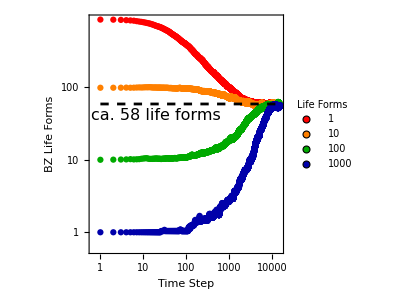

```mathematica
plot2=Show[{ListLogLogPlot[{Mean[popLifeForms1000],Mean[popLifeForms100],Mean[popLifeForms10],Mean[popLifeForms1]},PlotStyle-> {{Red,PointSize[0.015]},{Orange,PointSize[0.015]},{Darker[Green],PointSize[0.015]},{Darker[Blue],PointSize[0.015]}},PlotRange-> Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},Frame->True,AspectRatio->1,FrameLabel->{"Time Step","BZ Life Forms"},PlotLegends-> Placed[LineLegend[{"1","10","100","1000"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Life Forms",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.82,0.81}],ImageSize->300],LogLogPlot[avgSpecies,{i,1,15000},PlotStyle-> {Black,Dashing-> 0.02}],Graphics[Text[Style["ca. 58 life forms",16,Italic],{3,3.7}]]}]
```

```mathematica
Export[baseDirectory<>"plot2.png",plot2,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot2.png

```mathematica
Export[baseDirectory<>"plot2.svg",plot2]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot2.svg

```mathematica
Export[baseDirectory<>"plot2.pdf",plot2]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot2.pdf

## Creating Snapshots from the simulation

```mathematica
runID=10;nSteps=15000;
```

```mathematica
allPWMStates1=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[1]<>".mx"];
allPWMStates10=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[10]<>".mx"];allPWMStates100=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[100]<>".mx"];allPWMStates1000=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[1000]<>".mx"];
```

```mathematica
plotCells[timeStep_]:=Panel[GraphicsGrid[Partition[{MatrixPlot[allPWMStates1⟦timeStep⟧,PlotLabel-> "Initial Life Forms 1",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->15]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}],MatrixPlot[allPWMStates10⟦timeStep⟧,PlotLabel-> "Initial Life Forms 10",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->15]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}],MatrixPlot[allPWMStates100⟦timeStep⟧,PlotLabel-> "Initial Life Forms 100",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->15]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}],MatrixPlot[allPWMStates1000⟦timeStep⟧,PlotLabel-> "Initial Life Forms 1000",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->15]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},2],Spacings-> {0,10},Frame-> All,ImageSize->600],Style["Time Step: "<>ToString[timeStep],20],{{Top,Center}}]
```

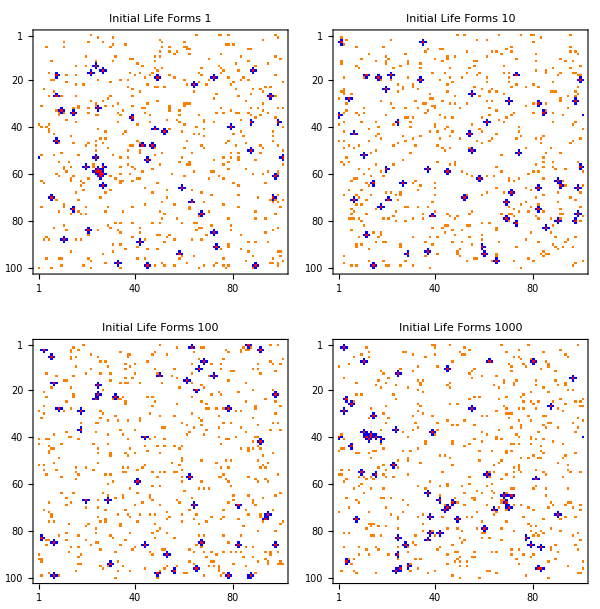
-Graphics-Time Step: 15000

```mathematica
plotCells[15000]
```

```mathematica
Export[baseDirectory<>"Image_"<>ToString[#]<>".png",plotCells[#],ImageResolution->100]&/@{1,10,100,500,1000,2500};
```

```mathematica
Export[baseDirectory<>"Image_"<>ToString[#]<>".svg",plotCells[#]]&/@{1,10,100,500,1000,2500};
```

```mathematica
Export[baseDirectory<>"Image_"<>ToString[#]<>".pdf",plotCells[#]]&/@{1,10,100,500,1000,2500};
```

## Correlations in BZ Life Forms

In this section, we estimate the spatial correlations between the living species and estimate the birth and death rates vs. time. The criteria to detect the emergence of new state from self-replication or propagation step consists of the following :

(1) Getting the list of cell states with PWM levels 3 at time step t and t+1
(2) Finding the still states which stays the same at t and t+1
(3) Getting list of new states formed at t+1 (states which were not present at t)
(4) If there is an appearance of new state and and nearest neighbour disappeared : Propagation
(5) If there is a next nearest neighbour present and no change in nearest neighbours : Replication

Please note that this is a simplified approach to estimate the statistics.

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/

```mathematica
nRuns=25;nSteps=15000;runID=25;nCells=100;
```

```mathematica
boundC[x_,y_]:={ Which[x==0,nCells,x==nCells+1,1,x>0&&x<nCells+1,x],Which[y== 0,nCells,y==nCells+1,1,y>0&&y<nCells+1,y]}
```

```mathematica
opTypes[PWMStates_,timeStep_]:=Block[{oldStates,newStates,stillStates,diff,oS, nS,nnList,nnnList,newStates1,newStates2,prop,rep,annh,comb1,comb2},
oldStates=Position[PWMStates⟦timeStep⟧,3]; 
newStates=Position[PWMStates⟦timeStep+1⟧,3];
diff=(Length@newStates-Length@oldStates);
stillStates=Intersection[oldStates,newStates];
oS=Delete[oldStates,Flatten[Position[oldStates,#]&/@stillStates,1]];(* Old States Disappered : Propagation and Annihiliation *)
nS=Delete[newStates,Flatten[Position[newStates,#]&/@stillStates,1]];
(* New States Appeared : Propagation and Replication *)
nnList={{#⟦1⟧-1,#⟦2⟧},{#⟦1⟧,#⟦2⟧-1},{#⟦1⟧+1,#⟦2⟧},{#⟦1⟧,#⟦2⟧+1}}&/@nS; 
nnnList={{#⟦1⟧-1,#⟦2⟧-1},{#⟦1⟧-1,#⟦2⟧+1},{#⟦1⟧+1,#⟦2⟧-1},{#⟦1⟧+1,#⟦2⟧+1}}&/@nS; 
nnList=Apply[boundC,nnList,{2}];
nnnList=Apply[boundC,nnnList,{2}];
newStates1=Table[{i,Length@Flatten[Position[oS,#]&/@nnList⟦i⟧]},{i,Length[nS]}];
newStates2=Table[{i,Length@Flatten[Position[oldStates,#]&/@nnnList⟦i⟧]},{i,Length[nS]}];
comb1=Length[Select[Table[If[newStates1⟦i,2⟧==0 && newStates2⟦i,2⟧== 0,1,0],{i,Length[nS]}],#==1&]];
comb2=Length[Select[Table[If[newStates1⟦i,2⟧>0 && newStates2⟦i,2⟧>0,1,0],{i,Length[nS]}],#==1&]];
prop=Length[Select[Table[If[newStates1⟦i,2⟧>0 && newStates2⟦i,2⟧== 0,1,0],{i,Length[nS]}],#== 1&]]+(comb1+comb2);
rep=Length[Select[Table[If[newStates1⟦i,2⟧==0 && newStates2⟦i,2⟧>0,1,0],{i,Length[nS]}],#==1&]]+(comb1+comb2);
annh=diff-rep;
{Length@nS,prop,rep,annh,comb1,comb2}
]
```

```mathematica
AnalyzeCells[nLifeForms_,runID_]:=Module[{PWMStates,outData},
PWMStates=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[nLifeForms]<>".mx"];
outData=Table[opTypes[PWMStates,timeStep],{timeStep,Length[PWMStates]-1}];
Return[outData]]
```

```mathematica
data1=Monitor[ParallelTable[AnalyzeCells[1,i],{i,nRuns}],i];
```

```mathematica
data2=Monitor[ParallelTable[AnalyzeCells[10,i],{i,nRuns}],i];
```

```mathematica
data3=Monitor[ParallelTable[AnalyzeCells[100,i],{i,nRuns}],i];
```

```mathematica
data4=Monitor[ParallelTable[AnalyzeCells[1000,i],{i,nRuns}],i];
```

```mathematica
Dimensions/@{data1,data2,data3,data4}
```

{{25,15000,6},{25,15000,6},{25,15000,6},{25,15000,6}}

```mathematica
p1a=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data1⟦All,All,2⟧],StandardDeviation[data1⟦All,All,2⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Propagation Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,25}],ListPlot[Mean[data1⟦All,All,2⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p1b=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data1⟦All,All,3⟧],StandardDeviation[data1⟦All,All,3⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,3}],ListPlot[Mean[data1⟦All,All,3⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p1c=Block[{dat=Table[Accumulate[data1⟦All,All,3⟧⟦i⟧],{i,Length@data1}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum.  Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,6000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p1d=Block[{dat=Table[Accumulate[data1⟦All,All,4⟧⟦i⟧],{i,Length@data1}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-6000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p1=GraphicsGrid[Partition[{p1a,p1b,p1c,p1d},2],Spacings->{-10,-10},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"Event_plot1.png",p1,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot1.png

```mathematica
Export[baseDirectory<>"Event_plot1.svg",p1]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot1.svg

```mathematica
Export[baseDirectory<>"Event_plot1.pdf",p1]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot1.pdf

```mathematica
p2a=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data2⟦All,All,2⟧],StandardDeviation[data2⟦All,All,2⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Propagation Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,30}],ListPlot[Mean[data2⟦All,All,2⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p2b=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data2⟦All,All,3⟧],StandardDeviation[data2⟦All,All,3⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,3}],ListPlot[Mean[data2⟦All,All,3⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p2c=Block[{dat=Table[Accumulate[data2⟦All,All,3⟧⟦i⟧],{i,Length@data2}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum.  Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,10000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p2d=Block[{dat=Table[Accumulate[data2⟦All,All,4⟧⟦i⟧],{i,Length@data2}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-10000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p2=GraphicsGrid[Partition[{p2a,p2b,p2c,p2d},2],Spacings->{-10,-10},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"Event_plot2.png",p2,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot2.png

```mathematica
Export[baseDirectory<>"Event_plot2.svg",p2]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot2.svg

```mathematica
Export[baseDirectory<>"Event_plot2.pdf",p2]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot2.pdf

```mathematica
p3a=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data3⟦All,All,2⟧],StandardDeviation[data3⟦All,All,2⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Propagation Events"},PlotMarkers->None,Frame-> True,PlotRange-> {10,40}],ListPlot[Mean[data3⟦All,All,2⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p3b=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data3⟦All,All,3⟧],StandardDeviation[data3⟦All,All,3⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,4}],ListPlot[Mean[data3⟦All,All,3⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p3c=Block[{dat=Table[Accumulate[data3⟦All,All,3⟧⟦i⟧],{i,Length@data3}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum.  Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,12000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p3d=Block[{dat=Table[Accumulate[data3⟦All,All,4⟧⟦i⟧],{i,Length@data3}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-12000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p3=GraphicsGrid[Partition[{p3a,p3b,p3c,p3d},2],Spacings->{-10,-10},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"Event_plot3.png",p3,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot3.png

```mathematica
Export[baseDirectory<>"Event_plot3.svg",p3]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot3.svg

```mathematica
Export[baseDirectory<>"Event_plot3.pdf",p3]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot3.pdf

```mathematica
p4a=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data4⟦All,All,2⟧],StandardDeviation[data4⟦All,All,2⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Propagation Events"},PlotMarkers->None,Frame-> True,PlotRange-> {10,40}],ListPlot[Mean[data4⟦All,All,2⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p4b=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data4⟦All,All,3⟧],StandardDeviation[data4⟦All,All,3⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,6}],ListPlot[Mean[data4⟦All,All,3⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p4c=Block[{dat=Table[Accumulate[data4⟦All,All,3⟧⟦i⟧],{i,Length@data4}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum.  Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,20000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p4d=Block[{dat=Table[Accumulate[data4⟦All,All,4⟧⟦i⟧],{i,Length@data4}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-20000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p4=GraphicsGrid[Partition[{p4a,p4b,p4c,p4d},2],Spacings->{-10,-10},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"Event_plot4.png",p4,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot4.png

```mathematica
Export[baseDirectory<>"Event_plot4.svg",p4]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot4.svg

```mathematica
Export[baseDirectory<>"Event_plot4.pdf",p4]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/Event_plot4.pdf

```mathematica
plot1=Block[{
dat1=Table[Accumulate[data1⟦All,All,3⟧⟦i⟧],{i,Length@data1}],
dat2=Table[Accumulate[data2⟦All,All,3⟧⟦i⟧],{i,Length@data2}],
dat3=Table[Accumulate[data3⟦All,All,3⟧⟦i⟧],{i,Length@data3}],
dat4=Table[Accumulate[data4⟦All,All,3⟧⟦i⟧],{i,Length@data4}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat1],StandardDeviation[dat1]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Red,Opacity[ 0.01]},FrameLabel->{"Time Step"," Cum. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat2],StandardDeviation[dat2]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Orange,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat3],StandardDeviation[dat3]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Green],Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat4],StandardDeviation[dat4]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Blue],Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,20000}],

ListPlot[{Mean[dat1],Mean[dat2],Mean[dat3],Mean[dat4]},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{{Red,PointSize[0.01]},{Orange,PointSize[0.01]},{Darker[Green],PointSize[0.01]},{Darker[Blue],PointSize[0.01]}},PlotLegends-> Placed[LineLegend[{"1","10","100","1000"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Life Forms",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.2,0.8}],PlotMarkers->None,Frame-> True]},ImageSize-> 300]]
```

```mathematica
Export[baseDirectory<>"plot_Rep.png",plot1,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot_Rep.png

```mathematica
Export[baseDirectory<>"plot_Rep.svg",plot1]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot_Rep.svg

```mathematica
Export[baseDirectory<>"plot_Rep.pdf",plot1]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot_Rep.pdf

```mathematica
plot2=Block[{
dat1=Table[Accumulate[data1⟦All,All,4⟧⟦i⟧],{i,Length@data1}],
dat2=Table[Accumulate[data2⟦All,All,4⟧⟦i⟧],{i,Length@data2}],
dat3=Table[Accumulate[data3⟦All,All,4⟧⟦i⟧],{i,Length@data3}],
dat4=Table[Accumulate[data4⟦All,All,4⟧⟦i⟧],{i,Length@data4}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat1],StandardDeviation[dat1]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Red,Opacity[ 0.01]},FrameLabel->{"Time Step"," Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat2],StandardDeviation[dat2]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Orange,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat3],StandardDeviation[dat3]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Green],Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat4],StandardDeviation[dat4]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Blue],Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-20000}],

ListPlot[{Mean[dat1],Mean[dat2],Mean[dat3],Mean[dat4]},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{{Red,PointSize[0.01]},{Orange,PointSize[0.01]},{Darker[Green],PointSize[0.01]},{Darker[Blue],PointSize[0.01]}},PlotLegends-> Placed[LineLegend[{"1","10","100","1000"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Life Forms",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.2,0.2}],PlotMarkers->None,Frame-> True]},ImageSize-> 300]]
```

```mathematica
Export[baseDirectory<>"plot_Death.png",plot2,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot_Death.png

```mathematica
Export[baseDirectory<>"plot_Death.svg",plot2]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot_Death.svg

```mathematica
Export[baseDirectory<>"plot_Death.pdf",plot2]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/plot_Death.pdf

```mathematica
plot3=Block[{
dat1=Table[Accumulate[data1⟦All,All,3⟧⟦i⟧]+Accumulate[data1⟦All,All,4⟧⟦i⟧],{i,Length@data1}],
dat2=Table[Accumulate[data2⟦All,All,3⟧⟦i⟧]+Accumulate[data2⟦All,All,4⟧⟦i⟧],{i,Length@data2}],
dat3=Table[Accumulate[data3⟦All,All,3⟧⟦i⟧]+Accumulate[data3⟦All,All,4⟧⟦i⟧],{i,Length@data3}],
dat4=Table[Accumulate[data4⟦All,All,3⟧⟦i⟧]+Accumulate[data4⟦All,All,4⟧⟦i⟧],{i,Length@data4}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat1],StandardDeviation[dat1]}],Axes-> False,AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Red,Opacity[ 0.01]},FrameLabel->{"Time Step","Net Cumulative Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-150,80}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat2],StandardDeviation[dat2]}],Axes-> False,AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Orange,Opacity[ 0.01]},FrameLabel->{"Time Step","Net Cumulative Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-150,80}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat3],StandardDeviation[dat3]}],Axes-> False,AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Green],Opacity[ 0.01]},FrameLabel->{"Time Step","Net Cumulative Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-150,80}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat4],StandardDeviation[dat4]}],Axes-> False,AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Blue],Opacity[ 0.01]},FrameLabel->{"Time Step","Net Cumulative Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-150,80}],

ListPlot[{Mean[dat1],Mean[dat2],Mean[dat3],Mean[dat4]},Joined-> True,Axes-> False,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{{Red,PointSize[0.01]},{Orange,PointSize[0.01]},{Darker[Green],PointSize[0.01]},{Darker[Blue],PointSize[0.01]}},PlotLegends-> Placed[LineLegend[{"1","10","100","1000"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Life Forms",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.8,0.2}],PlotMarkers->None,Frame-> True]},ImageSize-> 300]]
```

```mathematica
plot4=Block[{
dat1=Table[Accumulate[data1⟦All,All,3⟧⟦i⟧]+Accumulate[data1⟦All,All,4⟧⟦i⟧],{i,Length@data1}],
dat2=Table[Accumulate[data2⟦All,All,3⟧⟦i⟧]+Accumulate[data2⟦All,All,4⟧⟦i⟧],{i,Length@data2}],
dat3=Table[Accumulate[data3⟦All,All,3⟧⟦i⟧]+Accumulate[data3⟦All,All,4⟧⟦i⟧],{i,Length@data3}],
dat4=Table[Accumulate[data4⟦All,All,3⟧⟦i⟧]+Accumulate[data4⟦All,All,4⟧⟦i⟧],{i,Length@data4}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat1],StandardDeviation[dat1]}],AspectRatio->1,FrameTicks->{{{0,-400,-800},None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Red,Opacity[ 0.01]},FrameLabel->{"Time Step","Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-1000,80}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat2],StandardDeviation[dat2]}],AspectRatio->1,FrameTicks->{{{0,-400,-800},None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Orange,Opacity[ 0.01]},FrameLabel->{"Time Step","Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-1000,80}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat3],StandardDeviation[dat3]}],AspectRatio->1,FrameTicks->{{{0,-400,-800},None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Darker[Green],Opacity[ 0.01]},FrameLabel->{"Time Step","Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-1000,80}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat4],StandardDeviation[dat4]}],AspectRatio->1,FrameTicks->{{{0,-400,-800},None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Darker[Blue],Opacity[ 0.01]},FrameLabel->{"Time Step","Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-1000,80}],

ListPlot[{Mean[dat1],Mean[dat2],Mean[dat3],Mean[dat4]},Axes-> False,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{{Red,PointSize[0.01]},{Orange,PointSize[0.01]},{Darker[Green],PointSize[0.01]},{Darker[Blue],PointSize[0.01]}},ImageSize-> 50]}]]
```

```mathematica
plot5=Show[plot3,Graphics[Inset[plot4,{4500,-110}]]]
```

```mathematica
Export[baseDirectory<>"cum_events1.png",plot3,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/cum_events1.png

```mathematica
Export[baseDirectory<>"cum_events1.svg",plot3]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/cum_events1.svg

```mathematica
Export[baseDirectory<>"cum_events1.pdf",plot3]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/cum_events1.pdf

```mathematica
Export[baseDirectory<>"cum_events2.png",plot4,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/cum_events2.png

```mathematica
Export[baseDirectory<>"cum_events2.svg",plot4]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/cum_events2.svg

```mathematica
Export[baseDirectory<>"cum_events2.pdf",plot4]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/cum_events2.pdf

```mathematica
Export[baseDirectory<>"cum_events3.png",plot5,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/cum_events3.png

```mathematica
Export[baseDirectory<>"cum_events3.svg",plot5]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/cum_events3.svg

```mathematica
Export[baseDirectory<>"cum_events3.pdf",plot5]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/cum_events3.pdf

```mathematica
plot6=ListPlot[{Mean[data4⟦All,All,2⟧],Mean[data3⟦All,All,2⟧],Mean[data2⟦All,All,2⟧],Mean[data1⟦All,All,2⟧]},AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/3}],None}},PlotLegends-> Placed[LineLegend[{"1","10","100","1000"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Life Forms",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.8,0.2}],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},PlotRange-> {0,35},FrameLabel->{"Time Step","Propagation Events"},PlotStyle->{{Red,PointSize[0.01],Opacity[0.5]},{Orange,PointSize[0.01],Opacity[0.5]},{Darker[Green],PointSize[0.01],Opacity[0.5]},{Darker[Blue],PointSize[0.01],Opacity[0.5]}},PlotMarkers->None,Frame-> True,ImageSize->300]
```

```mathematica
plot7=ListLogPlot[{Mean[data1⟦All,All,2⟧],Mean[data2⟦All,All,2⟧],Mean[data3⟦All,All,2⟧],Mean[data4⟦All,All,2⟧]},AspectRatio->1,FrameTicks->{{{0,10,100},None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotRange-> Full,FrameLabel->{None,"Events"},PlotStyle->{{Darker[Blue],PointSize[0.01]},{Darker[Green],PointSize[0.01]},{Orange,PointSize[0.01]},{Red,PointSize[0.01]}},PlotMarkers->None,Frame-> True,ImageSize->140]
```

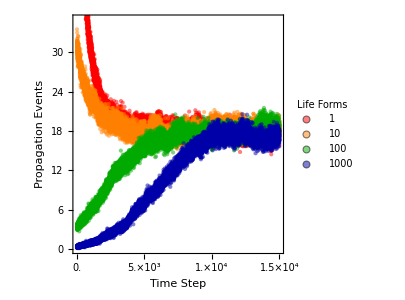
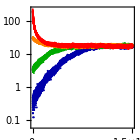

```mathematica
plot8=Show[plot6,Graphics[Inset[plot7,{10500,28}]]]
```

```mathematica
Export[baseDirectory<>"propg_events.png",plot8,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/propg_events.png

```mathematica
Export[baseDirectory<>"propg_events.svg",plot8]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/propg_events.svg

```mathematica
Export[baseDirectory<>"propg_events.pdf",plot8]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimInitPopulations/propg_events.pdf